# NC/GUP als H(r)-Modell

Mir ist ausgefallen, dass man auch die Modifikation der  1 = ∫|p⟩⟨p|→∫(d^3 p)/(1+βp^2)|p⟩⟨p| als H(r)-Modell auffassen kann. Das Integral der Modifikation ist dann eben H(r).
Achtung: Ich verwende hier n = Anzahl Extradimensionen, sodass mit d = Anzahl Gesamtdimensionen gilt: d = n+3 bei 3 normalen räumlichen Dimensionen.

## 0. Bestimmung von H(r)

Wie gesagt, das Integral der Modifikation ist H(r). In 3d, dann beliebigen Extradimensionen, einer Extradimension (man sieht die logarithmischen Korrekturen):

```mathematica
Integrate[ 1/(1 +β p^2),p]
```

ArcTan[p √β]/(√β)

```mathematica
(*Plot[ArcTan[p √β]/(√β),{p,-5,5}]~Manipulate~{{β,3.5},0,10}*)
```

```mathematica
Integrate[ 1/(1 +β p^(2+n)),p]
```

p Hypergeometric2F1[1,1/(2+n),1+1/(2+n),-p^(2+n) β]

```mathematica
Integrate[ 1/(1 +β p^(2+1)),p]
```

(2 √3 ArcTan[(-1+2 p β^(1/3))/(√3)]+2 Log[1+p β^(1/3)]-Log[1-p β^(1/3)+p^2 β^(2/3)])/(6 β^(1/3))

## 1. Klassischer Lösungsweg fürs Integral

Um nun dieses klassiche Fourierintegral ∫H'(x) e^(±ipx)d^D x zu lösen, versuche ich wieder auf meine alte Residuentechnik zurückzugreifen. Dafür zunächst ein Plausibilitätscheck, bereits mit skalierten Variablen β p→p

```mathematica
dH[p_,n_] = 1/(1 + p^(2+n));
Veff[p_,n_] = dH[p,n]HeavisideTheta[p] + (-1)^(n)  dH[-p,n]HeavisideTheta[-p];
hDPlus[p_,n_] = p^(1+n)*dH[p,n]
hDMinus[p_,n_] = p^(1+n)*dH[-p,n]
```

p^(1+n)/(1+p^(2+n))

p^(1+n)/(1+(-p)^(2+n))

### 1.0 Wie sehen die Funktionen aus?

```mathematica
myPlot[fun_] := Plot[Table[fun[z,n],{n,0,6}]//Evaluate,
{z,-2,2}, 
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLabel -> "Even and uneven functions "<>ToString[fun],
PlotLegends-> LineLegend[Table[n,{n,0,6}],LegendLabel-> "n="],
ImageSize-> Medium
]
```

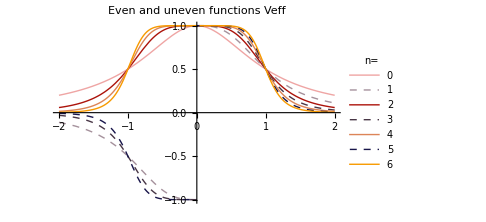
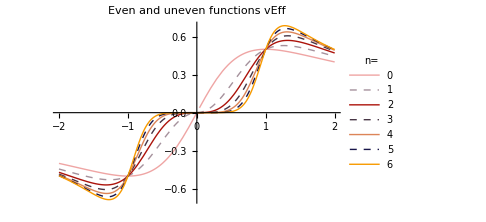

```mathematica
vEff[p_,n_] = p^(1+n)(dH[p,n]*HeavisideTheta[p] + (-1)^n  dH[-p,n]*HeavisideTheta[-p]);
myPlot@#&/@{Veff,vEff}
```

Alt:

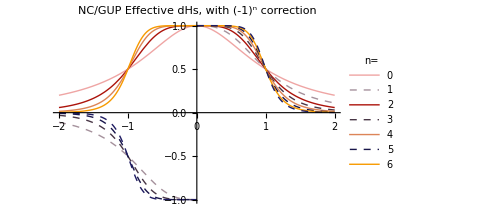

```mathematica
Plot[Evaluate@Table[Veff[p,n],{n,0,7}], {p,-2,2},
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLegends-> LineLegend[Table[n,{n,0,6}],
LegendLabel-> "n="],
PlotLabel -> "NC/GUP Effective dHs, with (-1)^n correction",
ImageSize-> Medium
]
```

### 1.1. Polstellen extrahieren

Code aus Calc13.

```mathematica
ReduceToSolutions[reduceResult_, extractVariable_] := Cases[reduceResult,Equal[extractVariable, value_]-> value, 100]
```

```mathematica
polReduce[n_, hDzSide_] := Reduce[Denominator@hDzSide[p,n]==0,p]
polstellen[n_,hDzSide_] := polReduce[n,hDzSide]~ ReduceToSolutions ~ p
poles[n_] := Join@@(polstellen[n,#[[1]]]~Select~#[[2]] &)/@{
hDPlus-> (Im[#]≤ 0 ∧Re[#] ≥ 0&),
 hDMinus-> (Im[#] ≤ 0 ∧ Re[#] ≤ 0&)
}
```

### 1.2. Plot der Polstellen

```mathematica
(* Zeichne die Polstellen.
Diese Funktion/Zelle ist aus Polstellen.nb kopiert und etwas modifiziert. *)
circle[s_Circle]:=s/.Circle[a_,r_,{start_,end_}]:>({s,Arrow[{#-r/10^2 {-Sin@end,Cos@end},#}]}&[a+r {Cos@end,Sin@end}])
Daten[n_] :={
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a}) , (* in Blau *)
{Re[#], Im[#]} & /@ polstellen[n, hDPlus],
{Re[#], Im[#]} & /@ polstellen[n, hDMinus],
{Re[#], Im[#]} & /@ poles[n] (* in Ringen *),
{Re[#], Im[#]} & /@ constructedPoles[n]
}
MakePlot[n_,
label_:"z*h(z) left and right roots vs unit roots. black: Residual taken Points"
] :=Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Blue, Opacity[0.6],Disk[]}], 0.1},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12},
{Graphics[{Red,Thickness[0.15],Circle[]}],0.18}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}],
Graphics@circle[Circle[{0,0},1,{0.1,Pi/(2+n) - 0.1 (* 0.1=our cirlce radius *)}]]
];
Manipulate[Show[
MakePlot[n],
Graphics[{Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{120,130},{0,0}]](*,
Text[Style[StringForm["# Residuen=``",ResidueList[n]//Length],{Black, 20}], Offset[{+30,-30},{0,0}]]*)}
]]
,{n,0,7,1}]
```

Nochmal eine Tabelle der Pole. Achtung bei meinem n, es entspricht nicht dem Knipfer-n. Das hier ist daher nicht umbedingt so richtig:

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# unique poles", "# poles","Unique Poles","Constructed Poles"}},
Table[{n,
Length@Union@poles[n],
Length@poles[n],
Union@poles[n] // Sort,
{"not yet"}
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # unique poles | # poles | Unique Poles | Constructed Poles
0 | 1 | 2 | {-ⅈ} | {not yet}
1 | 2 | 2 | {-(-1)^(1/3),-(-1)^(2/3)} | {not yet}
2 | 2 | 2 | {-(-1)^(1/4),-(-1)^(3/4)} | {not yet}
3 | 2 | 2 | {-(-1)^(1/5),-(-1)^(4/5)} | {not yet}
4 | 3 | 4 | {-ⅈ,-(-1)^(1/6),-(-1)^(5/6)} | {not yet}
5 | 4 | 4 | {-(-1)^(1/7),-(-1)^(3/7),-(-1)^(4/7),-(-1)^(6/7)} | {not yet}
6 | 4 | 4 | {-(-1)^(1/8),-(-1)^(3/8),-(-1)^(5/8),-(-1)^(7/8)} | {not yet}
7 | 4 | 4 | {-(-1)^(1/9),-(-1)^(1/3),-(-1)^(2/3),-(-1)^(8/9)} | {not yet}

### 1.3. Residuensatz ausführen

```mathematica
IntegralResidueList[n_] := 
(2 Pi I) * (-1)  * Residue[If[Re@# ≥ 0,hDPlus,hDMinus][p,n] * Exp[+I p z], {p,#}]& /@ poles[n]
```

```mathematica
poles[0]
```

{-ⅈ,-ⅈ}

```mathematica
hDPlus[p,0]
```

p/(1+p^2)

```mathematica
IntegralResidueList[0]
```

{-ⅈ ⅇ^z π,-ⅈ ⅇ^z π}

```mathematica
(*Integrate[ p / (I r)  * 1/(1 + β p^2) * (Exp[I r p] - Exp[- I r p]), {p,0,∞}]*)
```

ConditionalExpression[(ⅇ^(-Abs[r]/(√β)) π Sign[r])/(r β),r∈Reals&&(Re[1/β]≥0||1/β∉Reals)&&Re[1/(√β)]>0]

```mathematica
(*Integrate[ p^(2+1) / (I r)  * 1/(1 + β p^(2+1)) * (Exp[I r p] - Exp[- I r p]), {p,0,∞}]*)
```

```mathematica
WTF das integral macht komische
```

das integral komische macht WTF

```mathematica
IntegralValue[n_] := Total@IntegralResidueList[n]
TotalValue[z_,n_] :=  I / z * IntegralValue[n]
```

```mathematica
grid=Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# poles","Wert für A^-2(□)δ(z)"}},
Table[{n,
Length@poles[n],
TotalValue[z,n]  // Apart
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}, FrameStyle-> Directive[Gray,Thickness[0.05]]]
```

n | # poles | Wert für A^-2(□)δ(z)
0 | 2 | (2 ⅇ^z π)/z
1 | 2 | (2 ⅇ^((-1)^(1/6) z) π)/(3 z)-(2 ⅇ^(-(-1)^(5/6) z) π)/(3 z)
2 | 2 | (ⅇ^((-1)^(1/4) z) π)/(2 z)+(ⅇ^(-(-1)^(3/4) z) π)/(2 z)
3 | 2 | (2 ⅇ^((-1)^(3/10) z) π)/(5 z)-(2 ⅇ^(-(-1)^(7/10) z) π)/(5 z)
4 | 4 | (ⅇ^(-(-1)^(2/3) z) π)/(3 z)+((2 ⅇ^z+ⅇ^((-1)^(1/3) z)) π)/(3 z)
5 | 4 | -(2 ⅇ^(-(-1)^(13/14) z) π)/(7 z)+(2 ⅇ^(-(-1)^(9/14) z) (-1+ⅇ^((-1)^(1/14) z+(-1)^(9/14) z)+ⅇ^((-1)^(5/14) z+(-1)^(9/14) z)) π)/(7 z)
6 | 4 | (ⅇ^(-(-1)^(7/8) z) π)/(4 z)+(ⅇ^(-(-1)^(5/8) z) (1+ⅇ^((-1)^(1/8) z+(-1)^(5/8) z)+ⅇ^((-1)^(3/8) z+(-1)^(5/8) z)) π)/(4 z)
7 | 4 | -(2 ⅇ^(-(-1)^(5/6) z) π)/(9 z)+(2 ⅇ^(-(-1)^(11/18) z) (-1+ⅇ^((-1)^(1/6) z+(-1)^(11/18) z)+ⅇ^((-1)^(7/18) z+(-1)^(11/18) z)) π)/(9 z)

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../plots/A-table.pdf", grid]
```

../plots/A-table.pdf

Abgesehen von den Vorfaktoren und der Skalierung für z (β und so hier weggelassen) sieht das Ergebnis für n=0 eigentlich gut aus!
Es handelt sich bei dem Integral um das Massenintegral von Seite 2 des Papers.

```mathematica
(*Integrate[(2 ⅇ^z π)/z z^2,{z,0,Z}]*)
```

Leider ist das Integral für höhere n nicht mehr machbar. Oder doch?

```mathematica
(*Integrate[((2 ⅇ^((-1)^(1/6) z) π)/(3 z)-(2 ⅇ^(-(-1)^(5/6) z) π)/(3 z))z^3,{z,0,Z}] *)
```